# Generation of test data for Cu spd-Hamiltonian

```mathematica
Needs["GroupTheory`"];
```

```mathematica
dir=NotebookDirectory[];
```

```mathematica
SetDirectory[dir];
```

## spd-Hamiltonian

Read the Hamiltonian from file

```mathematica
SetDirectory[dir<>"../../../math"];
```

```mathematica
hfcc=GTReadFromFile["fcc_spd.ham"];
```

Read original parameter file for Cu

```mathematica
cu=GTTbDatabaseRetrieve["TB_Handbook","Cu"]
```

{{(ssσ)_1,-0.07518},{(spσ)_1,0.11571},{(ppσ)_1,0.19669},{(ppπ)_1,0.0194},{(sdσ)_1,-0.03107},{(pdσ)_1,-0.03289},{(pdπ)_1,0.01753},{(ddσ)_1,-0.02566},{(ddπ)_1,0.018},{(ddδ)_1,-0.00408},{(ssσ)_2,-0.00092},{(spσ)_2,0.01221},{(ppσ)_2,0.05389},{(ppπ)_2,0.00846},{(sdσ)_2,-0.00852},{(pdσ)_2,-0.00536},{(pdπ)_2,0.00321},{(ddσ)_2,-0.00451},{(ddπ)_2,0.00241},{(ddδ)_2,-0.00029},{(ss0),0.79466},{(pp0),1.35351},{(dd0),0.37},{(dd1),0.37307},{(dd2),0.3718},{(pd0),0.}}

Restrict to the parameters that occur in the Hamiltonian

```mathematica
cu1={{Subscript["(ssσ)", 1],-0.07518},{Subscript["(spσ)", 1],0.11571},{Subscript["(ppσ)", 1],0.19669},{Subscript["(ppπ)", 1],0.0194},{Subscript["(sdσ)", 1],-0.03107},{Subscript["(pdσ)", 1],-0.03289},{Subscript["(pdπ)", 1],0.01753},{Subscript["(ddσ)", 1],-0.02566},{Subscript["(ddπ)", 1],0.018},{Subscript["(ddδ)", 1],-0.00408},{Subscript["(ssσ)", 2],-0.00092},{Subscript["(spσ)", 2],0.01221},{Subscript["(ppσ)", 2],0.05389},{Subscript["(ppπ)", 2],0.00846},{Subscript["(sdσ)", 2],-0.00852},{Subscript["(pdσ)", 2],-0.00536},{Subscript["(pdπ)", 2],0.00321},{Subscript["(ddσ)", 2],-0.00451},{Subscript["(ddπ)", 2],0.00241},{Subscript["(ddδ)", 2],-0.00029},{"(ss0)",0.79466},{"(pp0)",1.35351},{"(dd0)",0.37}};
```

Export the parameter set to the directory for least squares fit (not really used there, but may be good for comparison)

```mathematica
SetDirectory[dir<>"/../fit/lsqr"];
```

```mathematica
parm1=GTTbParmExport[cu1,"cu_spd.parm","Cu-spd Papa",hfcc]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
(ssσ)_1 | (spσ)_1 | (ppσ)_1 | (ppπ)_1 | (sdσ)_1 | (pdσ)_1 | (pdπ)_1 | (ddσ)_1 | (ddπ)_1 | (ddδ)_1
-0.07518 | 0.11571 | 0.19669 | 0.0194 | -0.03107 | -0.03289 | 0.01753 | -0.02566 | 0.018 | -0.00408

11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
(ssσ)_2 | (spσ)_2 | (ppσ)_2 | (ppπ)_2 | (sdσ)_2 | (pdσ)_2 | (pdπ)_2 | (ddσ)_2 | (ddπ)_2 | (ddδ)_2
-0.00092 | 0.01221 | 0.05389 | 0.00846 | -0.00852 | -0.00536 | 0.00321 | -0.00451 | 0.00241 | -0.00029

21 | 22 | 23
(ss0) | (pp0) | (dd0)
0.79466 | 1.35351 | 0.37

{{(ssσ)_1,-0.07518},{(spσ)_1,0.11571},{(ppσ)_1,0.19669},{(ppπ)_1,0.0194},{(sdσ)_1,-0.03107},{(pdσ)_1,-0.03289},{(pdπ)_1,0.01753},{(ddσ)_1,-0.02566},{(ddπ)_1,0.018},{(ddδ)_1,-0.00408},{(ssσ)_2,-0.00092},{(spσ)_2,0.01221},{(ppσ)_2,0.05389},{(ppπ)_2,0.00846},{(sdσ)_2,-0.00852},{(pdσ)_2,-0.00536},{(pdπ)_2,0.00321},{(ddσ)_2,-0.00451},{(ddπ)_2,0.00241},{(ddδ)_2,-0.00029},{(ss0),0.79466},{(pp0),1.35351},{(dd0),0.37}}

Export the parameters as a Mathematica array

```mathematica
GTWriteToFile["parm0.parm",parm1]
```

## Band structure data

### original band structure

parametrize Hamiltonian

```mathematica
hfccp= hfcc /. GTTbParmToRule[cu1];
```

calculate band structure

Maximum Abscissa = 4.48735

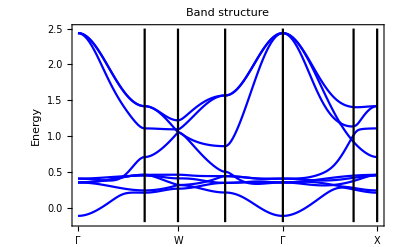

```mathematica
kp=GTBZPath["fcc"];
plt1=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotStyle->Blue,PlotRange->{{0,4.5},{-.2,2.5}}]
```

This is the complete band structure.  We restrict  the path to L-Γ-X for the fitting procedure.

```mathematica
kp1={{{1/2,1/2,1/2},{0,0,0},{0,0,1}},{"L","Γ","X"}};
```

Maximum Abscissa = 1.86603

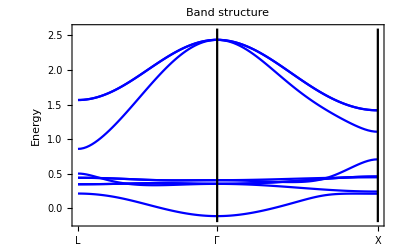

```mathematica
plt2=GTBandStructure[hfccp,kp1,50,9, Joined->True,PlotStyle->Blue,PlotRange->{{0,1.867},{-.2,2.6}}]
```

### Export band structure data

The  band structure data are copied to this directory and have to be copied to the directories where you need the sets for the fit.

#### Definition of k-points

set of symmetry points

```mathematica
kp=GTBZPath["fcc"];kpsym=kp[[1]];
```

points along the complete band structure

```mathematica
kpl=GTBZLines[kp,{8,8,8,8,8,8}];kpline1=Transpose[kpl[[1]]][[3]];
```

two lines only

```mathematica
kpl2=GTBZLines[kp1,{15,15}];kpline2=Transpose[kpl2[[1]]][[3]];
```

#### Symmetry points

```mathematica
bands0=GTBands[hfccp,kpsym,9,GOPlotBands->False,GOVerbose->True];
```

k-point | Eigenvalues |  |  |  |  |  |  |  | 
{0,0,0} | -0.1130 |  0.3537 |  0.3537 |  0.3537 |  0.4067 |  0.4067 |  2.4370 |  2.4370 |  2.4370
{0,0,1} |  0.2111 |  0.2423 |  0.4485 |  0.4601 |  0.4601 |  0.7084 |  1.1070 |  1.4180 |  1.4180
{0,1/2,1} |  0.2667 |  0.3178 |  0.3178 |  0.4104 |  0.4613 |  1.0530 |  1.0530 |  1.0950 |  1.2200
{1/2,1/2,1/2} |  0.2134 |  0.3478 |  0.3478 |  0.4417 |  0.4417 |  0.5027 |  0.8594 |  1.5660 |  1.5660
{0,0,0} | -0.1130 |  0.3537 |  0.3537 |  0.3537 |  0.4067 |  0.4067 |  2.4370 |  2.4370 |  2.4370
{3/4,3/4,0} |  0.2563 |  0.2775 |  0.3741 |  0.4187 |  0.4485 |  0.9191 |  1.0150 |  1.1370 |  1.4050
{1,1,0} |  0.2111 |  0.2423 |  0.4485 |  0.4601 |  0.4601 |  0.7084 |  1.1070 |  1.4180 |  1.4180

```mathematica
GTTbFitExport["energ.sy",bands0];
```

number of k-points = 7

number of bands    = 9

#### Symmetry lines

```mathematica
bands1=GTBands[hfccp,kpline1,9,GOPlotBands->False,GOVerbose->True];
```

k-point | Eigenvalues |  |  |  |  |  |  |  | 
{0,0,0} | -0.1130 |  0.3537 |  0.3537 |  0.3537 |  0.4067 |  0.4067 |  2.4370 |  2.4370 |  2.4370
{0,0,1/7} | -0.0914 |  0.3484 |  0.3571 |  0.3571 |  0.4017 |  0.4090 |  2.3490 |  2.3800 |  2.3800
{0,0,2/7} | -0.0327 |  0.3334 |  0.3677 |  0.3677 |  0.3897 |  0.4153 |  2.1230 |  2.2250 |  2.2250
{0,0,3/7} |  0.0497 |  0.3115 |  0.3797 |  0.3854 |  0.3854 |  0.4241 |  1.8440 |  2.0090 |  2.0090
{0,0,4/7} |  0.1406 |  0.2867 |  0.3896 |  0.4088 |  0.4088 |  0.4333 |  1.5860 |  1.7830 |  1.7830
{0,0,5/7} |  0.2011 |  0.2640 |  0.4334 |  0.4334 |  0.4413 |  0.4649 |  1.3750 |  1.5900 |  1.5900
{0,0,6/7} |  0.2124 |  0.2481 |  0.4466 |  0.4527 |  0.4527 |  0.6124 |  1.2000 |  1.4620 |  1.4620
{0,0,1} |  0.2111 |  0.2423 |  0.4485 |  0.4601 |  0.4601 |  0.7084 |  1.1070 |  1.4180 |  1.4180
{0,1/14,1} |  0.2135 |  0.2440 |  0.4470 |  0.4531 |  0.4602 |  0.7194 |  1.1070 |  1.4080 |  1.4080
{0,1/7,1} |  0.2205 |  0.2489 |  0.4350 |  0.4427 |  0.4603 |  0.7496 |  1.1040 |  1.3780 |  1.3810
{0,3/14,1} |  0.2310 |  0.2571 |  0.4115 |  0.4360 |  0.4606 |  0.7937 |  1.1010 |  1.3320 |  1.3410
{0,2/7,1} |  0.2432 |  0.2683 |  0.3864 |  0.4277 |  0.4608 |  0.8480 |  1.0980 |  1.2730 |  1.2970
{0,5/14,1} |  0.2548 |  0.2823 |  0.3619 |  0.4193 |  0.4611 |  0.9104 |  1.0960 |  1.2030 |  1.2580
{0,3/7,1} |  0.2634 |  0.2988 |  0.3389 |  0.4129 |  0.4612 |  0.9793 |  1.0950 |  1.1290 |  1.2300
{0,1/2,1} |  0.2667 |  0.3178 |  0.3178 |  0.4104 |  0.4613 |  1.0530 |  1.0530 |  1.0950 |  1.2200
{1/14,1/2,13/14} |  0.2705 |  0.3127 |  0.3206 |  0.4092 |  0.4579 |  0.9974 |  1.0020 |  1.1590 |  1.2690
{1/7,1/2,6/7} |  0.2816 |  0.2984 |  0.3290 |  0.4037 |  0.4506 |  0.8979 |  0.9512 |  1.2500 |  1.3490
{3/14,1/2,11/14} |  0.2778 |  0.2981 |  0.3424 |  0.3915 |  0.4451 |  0.7937 |  0.9136 |  1.3450 |  1.4240
{2/7,1/2,5/7} |  0.2547 |  0.3167 |  0.3610 |  0.3756 |  0.4428 |  0.6956 |  0.8879 |  1.4320 |  1.4850
{5/14,1/2,9/14} |  0.2335 |  0.3333 |  0.3610 |  0.3859 |  0.4420 |  0.6094 |  0.8714 |  1.5040 |  1.5300
{3/7,1/2,4/7} |  0.2187 |  0.3441 |  0.3512 |  0.4175 |  0.4417 |  0.5397 |  0.8623 |  1.5500 |  1.5570
{1/2,1/2,1/2} |  0.2134 |  0.3478 |  0.3478 |  0.4417 |  0.4417 |  0.5027 |  0.8594 |  1.5660 |  1.5660
{3/7,3/7,3/7} |  0.1989 |  0.3497 |  0.3497 |  0.4384 |  0.4384 |  0.4477 |  0.9836 |  1.6100 |  1.6100
{5/14,5/14,5/14} |  0.1561 |  0.3546 |  0.3546 |  0.3769 |  0.4293 |  0.4293 |  1.2500 |  1.7300 |  1.7300
{2/7,2/7,2/7} |  0.0906 |  0.3410 |  0.3607 |  0.3607 |  0.4174 |  0.4174 |  1.5720 |  1.9050 |  1.9050
{3/14,3/14,3/14} |  0.0163 |  0.3338 |  0.3642 |  0.3642 |  0.4074 |  0.4074 |  1.8990 |  2.0990 |  2.0990
{1/7,1/7,1/7} | -0.0505 |  0.3407 |  0.3615 |  0.3615 |  0.4043 |  0.4043 |  2.1800 |  2.2730 |  2.2730
{1/14,1/14,1/14} | -0.0966 |  0.3498 |  0.3561 |  0.3561 |  0.4057 |  0.4057 |  2.3700 |  2.3940 |  2.3940
{0,0,0} | -0.1130 |  0.3537 |  0.3537 |  0.3537 |  0.4067 |  0.4067 |  2.4370 |  2.4370 |  2.4370
{3/28,3/28,0} | -0.0886 |  0.3478 |  0.3572 |  0.3575 |  0.4031 |  0.4075 |  2.3380 |  2.3730 |  2.3730
{3/14,3/14,0} | -0.0224 |  0.3336 |  0.3628 |  0.3683 |  0.3940 |  0.4145 |  2.0780 |  2.1920 |  2.1990
{9/28,9/28,0} |  0.0696 |  0.3189 |  0.3587 |  0.3842 |  0.3847 |  0.4389 |  1.7500 |  1.9300 |  1.9640
{3/7,3/7,0} |  0.1709 |  0.3121 |  0.3427 |  0.3807 |  0.4025 |  0.4870 |  1.4550 |  1.6330 |  1.7300
{15/28,15/28,0} |  0.2552 |  0.3185 |  0.3186 |  0.3855 |  0.4206 |  0.5840 |  1.2580 |  1.3470 |  1.5480
{9/14,9/14,0} |  0.2814 |  0.2945 |  0.3393 |  0.3993 |  0.4364 |  0.7721 |  1.1050 |  1.1590 |  1.4420
{3/4,3/4,0} |  0.2563 |  0.2775 |  0.3741 |  0.4187 |  0.4485 |  0.9191 |  1.0150 |  1.1370 |  1.4050
{11/14,11/14,0} |  0.2468 |  0.2697 |  0.3884 |  0.4254 |  0.4516 |  0.8693 |  1.0720 |  1.1610 |  1.4030
{23/28,23/28,0} |  0.2376 |  0.2621 |  0.4037 |  0.4317 |  0.4542 |  0.8252 |  1.0940 |  1.2180 |  1.4040
{6/7,6/7,0} |  0.2290 |  0.2553 |  0.4194 |  0.4373 |  0.4563 |  0.7869 |  1.1000 |  1.2830 |  1.4070
{25/28,25/28,0} |  0.2216 |  0.2497 |  0.4345 |  0.4420 |  0.4580 |  0.7549 |  1.1040 |  1.3390 |  1.4110
{13/14,13/14,0} |  0.2159 |  0.2456 |  0.4455 |  0.4476 |  0.4592 |  0.7300 |  1.1060 |  1.3820 |  1.4140
{27/28,27/28,0} |  0.2123 |  0.2432 |  0.4477 |  0.4568 |  0.4599 |  0.7140 |  1.1070 |  1.4080 |  1.4170
{1,1,0} |  0.2111 |  0.2423 |  0.4485 |  0.4601 |  0.4601 |  0.7084 |  1.1070 |  1.4180 |  1.4180

```mathematica
GTTbFitExport["energ.li",bands1];
```

number of k-points = 43

number of bands    = 9

### Two lines only

```mathematica
bands2=GTBands[hfccp,kpline2,9,GOPlotBands->False,GOVerbose->True];
```

k-point | Eigenvalues |  |  |  |  |  |  |  | 
{1/2,1/2,1/2} |  0.2134 |  0.3478 |  0.3478 |  0.4417 |  0.4417 |  0.5027 |  0.8594 |  1.5660 |  1.5660
{13/28,13/28,13/28} |  0.2098 |  0.3483 |  0.3483 |  0.4408 |  0.4408 |  0.4853 |  0.8943 |  1.5770 |  1.5770
{3/7,3/7,3/7} |  0.1989 |  0.3497 |  0.3497 |  0.4384 |  0.4384 |  0.4477 |  0.9836 |  1.6100 |  1.6100
{11/28,11/28,11/28} |  0.1809 |  0.3518 |  0.3518 |  0.4087 |  0.4344 |  0.4344 |  1.1060 |  1.6620 |  1.6620
{5/14,5/14,5/14} |  0.1561 |  0.3546 |  0.3546 |  0.3769 |  0.4293 |  0.4293 |  1.2500 |  1.7300 |  1.7300
{9/28,9/28,9/28} |  0.1255 |  0.3545 |  0.3577 |  0.3577 |  0.4235 |  0.4235 |  1.4080 |  1.8130 |  1.8130
{2/7,2/7,2/7} |  0.0906 |  0.3410 |  0.3607 |  0.3607 |  0.4174 |  0.4174 |  1.5720 |  1.9050 |  1.9050
{1/4,1/4,1/4} |  0.0535 |  0.3348 |  0.3631 |  0.3631 |  0.4118 |  0.4118 |  1.7380 |  2.0020 |  2.0020
{3/14,3/14,3/14} |  0.0163 |  0.3338 |  0.3642 |  0.3642 |  0.4074 |  0.4074 |  1.8990 |  2.0990 |  2.0990
{5/28,5/28,5/28} | -0.0190 |  0.3363 |  0.3636 |  0.3636 |  0.4050 |  0.4050 |  2.0480 |  2.1910 |  2.1910
{1/7,1/7,1/7} | -0.0505 |  0.3407 |  0.3615 |  0.3615 |  0.4043 |  0.4043 |  2.1800 |  2.2730 |  2.2730
{3/28,3/28,3/28} | -0.0769 |  0.3455 |  0.3587 |  0.3587 |  0.4048 |  0.4048 |  2.2890 |  2.3420 |  2.3420
{1/14,1/14,1/14} | -0.0966 |  0.3498 |  0.3561 |  0.3561 |  0.4057 |  0.4057 |  2.3700 |  2.3940 |  2.3940
{1/28,1/28,1/28} | -0.1089 |  0.3527 |  0.3543 |  0.3543 |  0.4065 |  0.4065 |  2.4200 |  2.4260 |  2.4260
{0,0,0} | -0.1130 |  0.3537 |  0.3537 |  0.3537 |  0.4067 |  0.4067 |  2.4370 |  2.4370 |  2.4370
{0,0,1/14} | -0.1075 |  0.3523 |  0.3545 |  0.3545 |  0.4054 |  0.4073 |  2.4140 |  2.4230 |  2.4230
{0,0,1/7} | -0.0914 |  0.3484 |  0.3571 |  0.3571 |  0.4017 |  0.4090 |  2.3490 |  2.3800 |  2.3800
{0,0,3/14} | -0.0659 |  0.3420 |  0.3615 |  0.3615 |  0.3961 |  0.4117 |  2.2480 |  2.3130 |  2.3130
{0,0,2/7} | -0.0327 |  0.3334 |  0.3677 |  0.3677 |  0.3897 |  0.4153 |  2.1230 |  2.2250 |  2.2250
{0,0,5/14} |  0.0063 |  0.3231 |  0.3757 |  0.3757 |  0.3837 |  0.4195 |  1.9840 |  2.1210 |  2.1210
{0,0,3/7} |  0.0497 |  0.3115 |  0.3797 |  0.3854 |  0.3854 |  0.4241 |  1.8440 |  2.0090 |  2.0090
{0,0,1/2} |  0.0956 |  0.2992 |  0.3802 |  0.3966 |  0.3966 |  0.4288 |  1.7090 |  1.8940 |  1.8940
{0,0,4/7} |  0.1406 |  0.2867 |  0.3896 |  0.4088 |  0.4088 |  0.4333 |  1.5860 |  1.7830 |  1.7830
{0,0,9/14} |  0.1780 |  0.2748 |  0.4156 |  0.4213 |  0.4213 |  0.4376 |  1.4750 |  1.6800 |  1.6800
{0,0,5/7} |  0.2011 |  0.2640 |  0.4334 |  0.4334 |  0.4413 |  0.4649 |  1.3750 |  1.5900 |  1.5900
{0,0,11/14} |  0.2106 |  0.2549 |  0.4442 |  0.4442 |  0.4444 |  0.5345 |  1.2830 |  1.5160 |  1.5160
{0,0,6/7} |  0.2124 |  0.2481 |  0.4466 |  0.4527 |  0.4527 |  0.6124 |  1.2000 |  1.4620 |  1.4620
{0,0,13/14} |  0.2116 |  0.2438 |  0.4480 |  0.4582 |  0.4582 |  0.6796 |  1.1350 |  1.4290 |  1.4290
{0,0,1} |  0.2111 |  0.2423 |  0.4485 |  0.4601 |  0.4601 |  0.7084 |  1.1070 |  1.4180 |  1.4180

```mathematica
GTTbFitExport["energ.lis",bands2];
```

number of k-points = 29

number of bands    = 9

## Noisy parameters

### set 1 [-0.02,+0.02]

generate a number of equally distributed random numbers

```mathematica
rd=RandomReal[{-.02,.02},23]
```

{0.015355,-0.00924067,-0.00159211,-0.0190812,0.00060887,-0.0189386,-0.0161604,-0.00608799,-0.0043081,0.00852678,0.00439689,-0.00490494,-0.0130591,-0.00510222,0.0141744,-0.0148529,-0.0129828,-0.00168759,-0.01871,-0.0103076,0.00348533,-0.00295955,0.0161892}

for the calculations this fixed set of random numbers is used

```mathematica
rd1={-0.001572852586648188,-0.004678593165484093,-0.008121612198564672,-0.01927133906791082,0.008101299215994812,-0.0057060599311347104,0.009336279673436323,-0.0025662123773747894,0.015355288435744324,-0.014873036441598098,-0.0006273561718594806,-0.00234119137693848,0.00958986422205009,-0.0028837239593055702,-0.014478477073200699,0.01815409498201004,0.008548906169478926,-0.011493469167795534,0.009140560197095027,-0.013240091195798553,0.00150722891197929,-0.013654622647942226,-0.0035691829020934596};
```

generate the noisy parameter set

```mathematica
{pn,parms}=Transpose[cu1];cu1n={pn,parms+rd1}//Transpose;
```

calculate band structure with noisy parameters

Maximum Abscissa = 4.48735

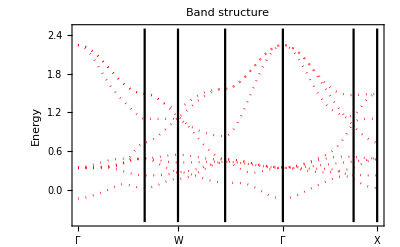

```mathematica
hfccp= hfcc /. GTTbParmToRule[cu1n];
plt3=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotRange->{{0,4.5},{-.5,2.5}},PlotStyle->{{Red,Dotted}}]
```

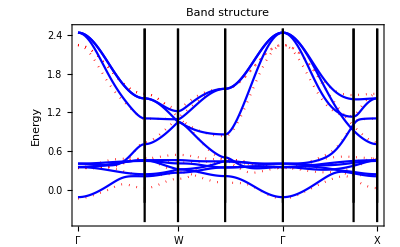

```mathematica
Show[plt3,plt1]
```

Maximum Abscissa = 1.86603

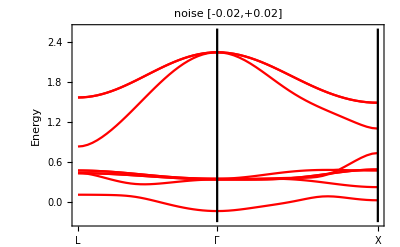

```mathematica
hfccp= hfcc /. GTTbParmToRule[cu1n];
plt4=GTBandStructure[hfccp,kp1,30,9, Joined->True,PlotRange->{{0,1.867},{-.3,2.6}},PlotStyle->Red,PlotLabel->"noise [-0.02,+0.02]"]
```

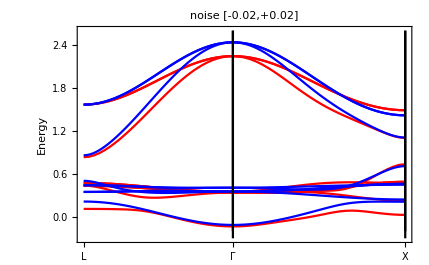

```mathematica
Show[plt4,plt2]
```

The band structure with the noisy parameters is relatively close to the correct one. This corresponds to the situation, that we have guessed a  good first approximation.

export the  noisy parameters

```mathematica
parm2=GTTbParmExport[cu1n,"cu_spdn1.parm","Cu_spd Papa (-0.02,0.02)",hfcc];
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
(ssσ)_1 | (spσ)_1 | (ppσ)_1 | (ppπ)_1 | (sdσ)_1 | (pdσ)_1 | (pdπ)_1 | (ddσ)_1 | (ddπ)_1 | (ddδ)_1
-0.0767529 | 0.111031 | 0.188568 | 0.000128661 | -0.0229687 | -0.0385961 | 0.0268663 | -0.0282262 | 0.0333553 | -0.018953

11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
(ssσ)_2 | (spσ)_2 | (ppσ)_2 | (ppπ)_2 | (sdσ)_2 | (pdσ)_2 | (pdπ)_2 | (ddσ)_2 | (ddπ)_2 | (ddδ)_2
-0.00154736 | 0.00986881 | 0.0634799 | 0.00557628 | -0.0229985 | 0.0127941 | 0.0117589 | -0.0160035 | 0.0115506 | -0.0135301

21 | 22 | 23
(ss0) | (pp0) | (dd0)
0.796167 | 1.33986 | 0.366431

```mathematica
GTWriteToFile["parm1.parm",parm2]
```

### set 1 [-0.05,+0.05]

We want to create a set with stronger deviations to the original band structure.

generate a number of equally distributed random numbers

```mathematica
rd=RandomReal[{-.05,.05},23]
```

{-0.0445083,-0.0173225,0.0464994,-0.0359527,-0.0327255,-0.0424965,-0.0398851,0.0402975,0.0366089,0.0190425,-0.00130579,0.0355851,0.0122776,-0.0394621,-0.0492127,-0.0287216,0.0327533,0.0143529,0.021181,-0.000868691,0.00608458,-0.0176918,-0.0356635}

for the calculations this fixed set of random numbers is used

```mathematica
rd1={-0.04102785701804265,-0.021886033043217817,-0.03666131734492263,0.011034309362124656,0.02874658204277633,0.0371948599610358,-0.022105476554644454,-0.039050230148279394,-0.016562958619336182,0.008533306739915841,0.03358215511498616,0.008411122609171123,0.049097424001748685,-0.005220967520933428,0.002759652577809163,0.017992441647356666,0.03897391739309347,-0.02738216228355292,-0.00016681580679722696,-0.04535351991512512,-0.02508690180587711,-0.04694722941877322,0.04918192141941563}
```

{-0.0410279,-0.021886,-0.0366613,0.0110343,0.0287466,0.0371949,-0.0221055,-0.0390502,-0.016563,0.00853331,0.0335822,0.00841112,0.0490974,-0.00522097,0.00275965,0.0179924,0.0389739,-0.0273822,-0.000166816,-0.0453535,-0.0250869,-0.0469472,0.0491819}

generate the noisy parameter set

```mathematica
{pn,parms}=Transpose[cu1];cu1n={pn,parms+rd1}//Transpose;
```

calculate band structure with noisy parameters

Maximum Abscissa = 4.48735

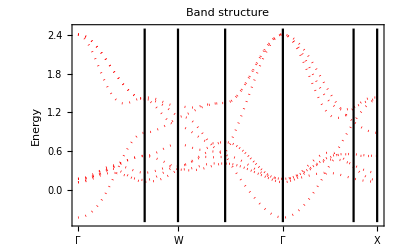

```mathematica
hfccp= hfcc /. GTTbParmToRule[cu1n];
plt3=GTBandStructure[hfccp,kp,30,9, Joined->True,PlotRange->{{0,4.5},{-.5,2.5}},PlotStyle->{{Red,Dotted}}]
```

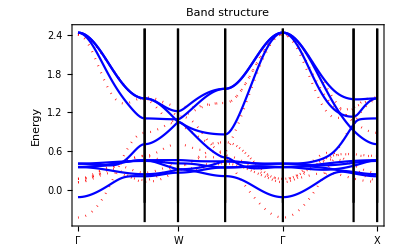

```mathematica
Show[plt3,plt1]
```

Maximum Abscissa = 1.86603

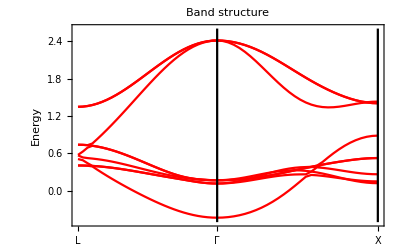

```mathematica
hfccp= hfcc /. GTTbParmToRule[cu1n];
plt4=GTBandStructure[hfccp,kp1,30,9, Joined->True,PlotRange->{{0,1.867},{-.5,2.6}},PlotStyle->Red]
```

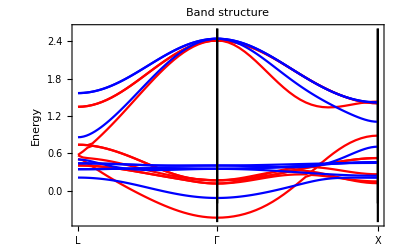

```mathematica
Show[plt4,plt2]
```

The band structure with the noisy parameters shows now stronger deviations. This corresponds to the situation, that we have guessed a a bad first approximation.

export the  noisy parameters

```mathematica
parm2=GTTbParmExport[cu1n,"cu_spdn2.parm","Cu_spd Papa (-0.05,0.05)",hfcc];
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
(ssσ)_1 | (spσ)_1 | (ppσ)_1 | (ppπ)_1 | (sdσ)_1 | (pdσ)_1 | (pdπ)_1 | (ddσ)_1 | (ddπ)_1 | (ddδ)_1
-0.116208 | 0.093824 | 0.160029 | 0.0304343 | -0.00232342 | 0.00430486 | -0.00457548 | -0.0647102 | 0.00143704 | 0.00445331

11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
(ssσ)_2 | (spσ)_2 | (ppσ)_2 | (ppπ)_2 | (sdσ)_2 | (pdσ)_2 | (pdπ)_2 | (ddσ)_2 | (ddπ)_2 | (ddδ)_2
0.0326622 | 0.0206211 | 0.102987 | 0.00323903 | -0.00576035 | 0.0126324 | 0.0421839 | -0.0318922 | 0.00224318 | -0.0456435

21 | 22 | 23
(ss0) | (pp0) | (dd0)
0.769573 | 1.30656 | 0.419182

```mathematica
GTWriteToFile["parm2.parm",parm2]
```